### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 3; blocks = 4; l = 100;
(*------------------------*)
data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
upKer = RandomInteger[{-16,16},td*6];
```

```mathematica
expected=ListConvolve[Reverse[ker],data,1,0];
```

```mathematica
Max[Abs[expected]]
```

958

```mathematica
Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upKer]];
```

### After simulation:

```mathematica
ker
```

{-8,-11,12,-6,-12,-6,15,3,-10,6,14,4}

```mathematica
expected
```

{52,138,-76,-260,-111,-76,-193,-136,-393,53,-21,255,13,208,83,421,463,270,-512,49,126,-58,-503,93,205,141,293,30,-147,-187,282,89,-230,-527,88,451,-255,-317,290,404,262,-479,-108,118,-163,-331,-715,107,139,16,-214,241,350,532,-14,-240,700,-88,-475,-263,661,-432,-710,652,573,-730,-155,879,337,-459,269,648,18,-65,-13,61,37,4,-502,-43,258,-58,-958,125,331,56,-629,13,516,27,-103,-458,435,128,-198,-478,324,444,-556,-327}

```mathematica
upKer
```

{14,-10,11,12,-6,0,7,-14,16,-1,-13,14,-7,-8,15,7,7,-13}

```mathematica
Max[lol]
```

lol

```mathematica
upIn=Flatten@Riffle[expected,{ConstantArray[0,2]}]
```

{52,0,0,138,0,0,-76,0,0,-260,0,0,-111,0,0,-76,0,0,-193,0,0,-136,0,0,-393,0,0,53,0,0,-21,0,0,255,0,0,13,0,0,208,0,0,83,0,0,421,0,0,463,0,0,270,0,0,-512,0,0,49,0,0,126,0,0,-58,0,0,-503,0,0,93,0,0,205,0,0,141,0,0,293,0,0,30,0,0,-147,0,0,-187,0,0,282,0,0,89,0,0,-230,0,0,-527,0,0,88,0,0,451,0,0,-255,0,0,-317,0,0,290,0,0,404,0,0,262,0,0,-479,0,0,-108,0,0,118,0,0,-163,0,0,-331,0,0,-715,0,0,107,0,0,139,0,0,16,0,0,-214,0,0,241,0,0,350,0,0,532,0,0,-14,0,0,-240,0,0,700,0,0,-88,0,0,-475,0,0,-263,0,0,661,0,0,-432,0,0,-710,0,0,652,0,0,573,0,0,-730,0,0,-155,0,0,879,0,0,337,0,0,-459,0,0,269,0,0,648,0,0,18,0,0,-65,0,0,-13,0,0,61,0,0,37,0,0,4,0,0,-502,0,0,-43,0,0,258,0,0,-58,0,0,-958,0,0,125,0,0,331,0,0,56,0,0,-629,0,0,13,0,0,516,0,0,27,0,0,-103,0,0,-458,0,0,435,0,0,128,0,0,-198,0,0,-478,0,0,324,0,0,444,0,0,-556,0,0,-327}

```mathematica
lol=ListConvolve[Reverse[upKer],upIn,1,0]
```

{-676,364,364,-1014,550,602,3786,-2312,-1550,5004,-3734,-1062,-1313,47,2709,-4961,3452,2357,-2827,3416,-1508,-4803,5454,-4486,-3709,5176,-7110,-12797,9551,-559,-7446,8360,-4457,-11299,9512,-5206,2714,1300,-7922,-3598,1943,-3903,6886,-5226,1387,-1339,-1923,5015,7591,-6746,5393,10800,-9827,1487,26212,-20235,918,3784,-8909,13112,880,-3622,14391,231,-1133,4801,11187,-5009,-5262,-13182,8491,-1468,-8701,6796,3079,-4118,4268,-2994,2026,554,-5338,3726,-2365,-6473,9742,-9212,3217,7589,-7521,6303,-6498,1793,9130,1326,-254,2269,5611,-2788,-5168,7542,-4362,-4496,-12902,6754,5924,-12499,9170,6474,3859,1331,-10233,5488,-1812,-9813,-10676,6309,1339,-8452,4613,5974,6603,-3710,-249,17648,-10309,-10935,864,-4556,4205,-2478,-1075,12803,-843,413,3588,4664,-781,-4130,-1333,3548,-9701,-20546,13426,4848,-14210,13844,-1682,-9858,11235,-12227,3039,2669,-14214,-11760,7753,-4584,-2498,1176,4255,-187,-699,1673,17094,-11154,-4829,13604,-12690,232,-1733,-4956,17892,11910,-9592,5910,16667,-13597,2191,6108,-5117,3396,-23236,12338,11367,11949,-4715,-1969,6828,-2695,-11380,-19823,12934,4787,-17414,12737,1383,23124,-12248,-10673,4767,-3242,-6552,-22614,12049,9863,2126,-2396,7255,27151,-16516,-8274,370,-2902,-1168,-7128,-91,13849,15577,-12941,8458,18198,-13405,-136,4765,-5901,1684,1349,-5454,12251,6340,-5738,8678,1347,-669,-911,7365,-4153,-4218,-6466,2909,4018,-10292,7788,3935,-3603,4723,-5117,14552,-6022,-12827,-18201,10959,1901,-17241,13465,4488,-6503,7299,-5840,15013,-4576,-16559,-14062,8591,-5157,-13048,7665,10264,1148,1052,-2533,9792,-4613,-8099,6124,-3745,-7550,-13392,4444,12917,2477,-510,5136,3553,-1305,-6781,10863,-5738,-5981,-17144,8844,5516,-5987,4384,7558,12184,-5056,-11254,5133}

```mathematica
2^13
```

8192

```mathematica
Floor[lol/2^8]
```

{-3,1,1,-4,2,2,14,-10,-7,19,-15,-5,-6,0,10,-20,13,9,-12,13,-6,-19,21,-18,-15,20,-28,-50,37,-3,-30,32,-18,-45,37,-21,10,5,-31,-15,7,-16,26,-21,5,-6,-8,19,29,-27,21,42,-39,5,102,-80,3,14,-35,51,3,-15,56,0,-5,18,43,-20,-21,-52,33,-6,-34,26,12,-17,16,-12,7,2,-21,14,-10,-26,38,-36,12,29,-30,24,-26,7,35,5,-1,8,21,-11,-21,29,-18,-18,-51,26,23,-49,35,25,15,5,-40,21,-8,-39,-42,24,5,-34,18,23,25,-15,-1,68,-41,-43,3,-18,16,-10,-5,50,-4,1,14,18,-4,-17,-6,13,-38,-81,52,18,-56,54,-7,-39,43,-48,11,10,-56,-46,30,-18,-10,4,16,-1,-3,6,66,-44,-19,53,-50,0,-7,-20,69,46,-38,23,65,-54,8,23,-20,13,-91,48,44,46,-19,-8,26,-11,-45,-78,50,18,-69,49,5,90,-48,-42,18,-13,-26,-89,47,38,8,-10,28,106,-65,-33,1,-12,-5,-28,-1,54,60,-51,33,71,-53,-1,18,-24,6,5,-22,47,24,-23,33,5,-3,-4,28,-17,-17,-26,11,15,-41,30,15,-15,18,-20,56,-24,-51,-72,42,7,-68,52,17,-26,28,-23,58,-18,-65,-55,33,-21,-51,29,40,4,4,-10,38,-19,-32,23,-15,-30,-53,17,50,9,-2,20,13,-6,-27,42,-23,-24,-67,34,21,-24,17,29,47,-20,-44,20}

```mathematica
result
```

result

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

{}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
fker = Flatten@Import[RelativeDir["15l3.dat"]]
```

{-229,-211,135,1535,4358,8070,11299,12583,11299,8070,4358,1535,135,-211,-229}

```mathematica
fupker =  Flatten@Import[RelativeDir["12up3.dat"]]
```

{-495,-2217,-3163,7616,35148,61425,61425,35148,7616,-3163,-2217,-495}

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap16.dat"]];
```

```mathematica
afirIn = snaps[[2]]
```

{-59296,-55719,-55719,-55719,-51152,-51152,-51152,-45674,-45674,-45674,-39412,-39412,-39412,-32535,-32535,-32535,-25220,-25220,-25220,-17618,-17618,-17618,-9844,-9844,-9844,-1992,-1992,-1992,5854,5854,5854,13609,13609,13609,21193,21193,21193,28506,28506,28506,35416,35416,35416,41762,41762,41762,47381,47381,47381,52140}

```mathematica
afirOut = snaps[[10]]
```

{-3876,-3938,-3940,-3952,-3980,-3948,-3934,-3933,-3873,-3836,-3809,-3725,-3668,-3617,-3512,-3436,-3361,-3236,-3142,-3045,-2902,-2793,-2676,-2519,-2396,-2262,-2095,-1962,-1816,-1642,-1503,-1347,-1171,-1027,-863,-687,-541,-372,-198,-51,121,292,437,611,776,920,1093,1251,1390,1562}

```mathematica
expafirOut=Floor[ListConvolve[fupker, Flatten[Riffle[Downsample[afirIn,3],{{0,0}}]]]/2^20]
```

{-3236,-3142,-3045,-2902,-2793,-2676,-2519,-2396,-2262,-2095,-1962,-1816,-1642,-1503,-1347,-1171,-1027,-863,-687,-541,-372,-198,-51,121,292,437,611,776,920,1093,1251,1390,1562,1710,1843,2009,2145,2269}

```mathematica
LongestCommonSubsequence[afirOut,expafirOut]
```

{-3236,-3142,-3045,-2902,-2793,-2676,-2519,-2396,-2262,-2095,-1962,-1816,-1642,-1503,-1347,-1171,-1027,-863,-687,-541,-372,-198,-51,121,292,437,611,776,920,1093,1251,1390,1562}

```mathematica
firIn=Downsample[snaps[[1]],3,3]; firOut = Downsample[snaps[[2]],3,1];
```

```mathematica
Floor[ListConvolve[fker,firIn]/2^12]
```

{55256,49712}

```mathematica
firOut
```

{-59296,-55719,-51152,-45674,-39412,-32535,-25220,-17618,-9844,-1992,5854,13609,21193,28506,35416,41762,47381}

```mathematica
LongestCommonSubsequence[ListConvolve[ker,firIn],firOut]
```

{}

```mathematica
ListPlot[{firIn,firOutS},Joined->True]
```

ListPlot::lpn: {{{1.,3504.},{2.,3769.},{3.,3949.},{4.,4068.},{5.,4102.},{6.,4142.},{7.,4055.},{8.,3822.},{9.,3473.},{10.,2970.},{11.,2308.},{12.,1572.},{13.,848.},{14.,81.},{15.,-697.},{16.,-1385.}},{}} is not a list of numbers or pairs of numbers.

ListPlot[{{3504,3769,3949,4068,4102,4142,4055,3822,3473,2970,2308,1572,848,81,-697,-1385},firOutS},Joined→True]

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[42];
```

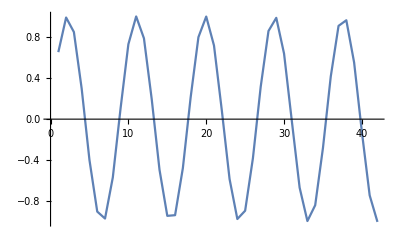

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Flatten@Riffle[in,{{0,0}}]
```

{0.651834,0,0,0.988652,0,0,0.847678,0,0,0.297042,0,0,-0.397148,0,0,-0.899405,0,0,-0.967001,0,0,-0.567269,0,0,0.106611,0,0,0.728969,0,0,0.999033,0,0,0.786288,0,0,0.193549,0,0,-0.492727,0,0,-0.940881,0,0,-0.934329,0,0,-0.476238,0,0,0.212007,0,0,0.797794,0,0,0.998027,0,0,0.715936,0,0,0.0878512,0,0,-0.58269,0,0,-0.971632,0,0,-0.891007,0,0,-0.379779,0,0,0.314987,0,0,0.857527,0,0,0.985645,0,0,0.637424,0,0,-0.0188484,0,0,-0.666012,0,0,-0.991308,0,0,-0.837528,0,0,-0.278991,0,0,0.414376,0,0,0.907484,0,0,0.962028,0,0,0.551646,0,0,-0.125333,0,0,-0.741742,0,0,-0.999684}

```mathematica
out=ListConvolve[fupker/2^16,inR,1,0]
```

{-0.00492337,-0.0220507,-0.0314598,0.0682828,0.316144,0.563229,0.719434,0.851143,0.961473,0.991441,0.952754,0.890137,0.784307,0.593921,0.388618,0.198137,-0.0519387,-0.30071,-0.483788,-0.672698,-0.844712,-0.93191,-0.968359,-0.980485,-0.929662,-0.796034,-0.642413,-0.47813,-0.239006,0.00612195,0.20447,0.433529,0.651698,0.788255,0.896549,0.982325,0.991096,0.926289,0.838217,0.714963,0.508375,0.289019,0.0933055,-0.155224,-0.399855,-0.573444,-0.743807,-0.895489,-0.963062,-0.972926,-0.958354,-0.887255,-0.731853,-0.558069,-0.382659,-0.137093,0.111917,0.306867,0.523921,0.727816,0.848092,0.931736,0.991979,0.979453,0.889265,0.776742,0.637469,0.417034,0.186125,-0.0125894,-0.25674,-0.494443,-0.656563,-0.806438,-0.936058,-0.983236,-0.966403,-0.925298,-0.834734,-0.659329,-0.467364,-0.282825,-0.0336167,0.216436,0.405767,0.608342,0.795638,0.898261,0.956303,0.990327,0.956647,0.842106,0.706414,0.552708,0.320939,0.081109,-0.118341,-0.35533,-0.583395,-0.732199,-0.859877,-0.965957,-0.992203,-0.948865,-0.881696,-0.772698,-0.57929,-0.371332,-0.179768,0.0702423,0.318488,0.500041,0.685828,0.85439,0.938191,0.96997,0.977386,0.922936,0.785348,0.628035,0.461648,0.221186,-0.0248311,-0.222743}

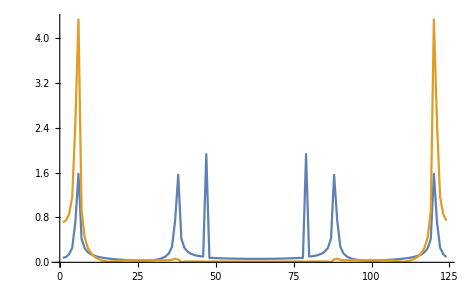

```mathematica
ListPlot[{Abs[Fourier[inR]],Abs[Fourier[out]]},Joined->True,PlotRange->All]
```

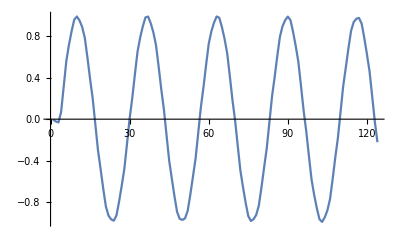

```mathematica
ListPlot[out,Joined->True]
```